# Exact Quasisymmetry

## Input Parameters

```mathematica
R0=1;sigma0=0;NFP=2;etab=0.7;
ns=10;nIts=50;tol=10^-5;nLineS=8;
(*Initial Axis*)
er1=0.04;ez1=0.04;
eR0=Prepend[Table[0.,{i,1,ns/2-1}],0.05];eZ0=eR0;
(*psi initial = psi31,psi32,psi33,psi34,sigma,F0*)
psiinit[t_]={0.01Cos[NFP t],0.01Sin[NFP t],0.01Cos[NFP t],0.01Sin[NFP t],0.01 Cos[NFP t],0.1};
```

## Axis Functions

```mathematica
R[x_]=R0+eR1 Cos[ NFP x]+Sum[eR[n] Cos[(n+1) NFP x],{n,1,ns/2}];
Z[x_]=eZ1 Sin[NFP x]+Sum[eZ[n] Sin[(n+1) NFP x],{n,1,ns/2}];
optsComp={Table[eR[n]->er[[n]],{n,1,ns/2}],Table[eZ[n]->ez[[n]],{n,1,ns/2}]}//Flatten//Quiet;
closedCurve[x_]={R[x]Cos[x],R[x]Sin[x],Z[x]};
 curvFunc1[x_]=Chop[ComplexExpand[Norm[Cross[closedCurve'[x], closedCurve''[x]]]]/ComplexExpand[Norm[closedCurve'[x]]^3],10^-6];
torsFunc1[x_]=Chop[Dot[Cross[closedCurve'[x], closedCurve''[x]], closedCurve'''[x]]/ComplexExpand[Norm[Cross[closedCurve'[x], closedCurve''[x]]]]^2,10^-6];
sprimeFunc1[x_]=Chop[ComplexExpand[Norm[closedCurve'[x]]],10^-6]//Quiet;
```

```mathematica
atemp=Compile[{{phi,_Real},{er,_Real,1},{ez,_Real,1},{eR1,_Real},{eZ1,_Real}},Evaluate[D[curvFunc1'''[phi],eR[1]]/.optsComp]]
```

CompiledFunction[{phi, er, ez, eR1, eZ1}, Block[{Compile`$2, Compile`$3, Compile`$5, Compile`$9, Compile`$11, Compile`$30, Compile`$12, Compile`$14, Compile`$15, Compile`$16, Compile`$18, Compile`$19, Compile`$20, Compile`$22, Compile`$23, <<5152>>, Compile`$7207, Compile`$7208, Compile`$7209, Compile`$7210, Compile`$7211, Compile`$7212, Compile`$7213}, <<1>>], -CompiledCode-]

```mathematica
atemp[1,eR0,eZ0,er1,ez1]//Timing
```

{0.000164,4796.54}

```mathematica
{curvFunc[phi_,er_,ez_,eR1_,eZ1_],curvFuncp[phi_,er_,ez_,eR1_,eZ1_],curvFuncpp[phi_,er_,ez_,eR1_,eZ1_],curvFuncppp[phi_,er_,ez_,eR1_,eZ1_]}={curvFunc1[phi],D[curvFunc1[phi],phi]/sprimeFunc1[phi],D[D[curvFunc1[phi],phi]/sprimeFunc1[phi],phi] 1/sprimeFunc1[phi],D[D[D[curvFunc1[phi],phi]/sprimeFunc1[phi],phi] 1/sprimeFunc1[phi],phi] 1/sprimeFunc1[phi]}/.optsComp//Quiet;
{torsFunc[phi_,er_,ez_,eR1_,eZ1_],torsFuncp[phi_,er_,ez_,eR1_,eZ1_],torsFuncpp[phi_,er_,ez_,eR1_,eZ1_]}={torsFunc1[phi],D[torsFunc1[phi],phi]/sprimeFunc1[phi],D[D[torsFunc1[phi],phi]/sprimeFunc1[phi],phi] 1/sprimeFunc1[phi]}/.optsComp//Quiet;
```

```mathematica
curvCA=Compile[{{phi,_Real},{er,_Real,1},{ez,_Real,1},{eR1,_Real},{eZ1,_Real}},Evaluate[{curvFunc[phi,er,ez,eR1,eZ1],curvFuncp[phi,er,ez,eR1,eZ1],curvFuncpp[phi,er,ez,eR1,eZ1],curvFuncppp[phi,er,ez,eR1,eZ1]}],CompilationTarget->"C",Parallelization->True,RuntimeAttributes->{Listable},RuntimeOptions->"Speed"]//Quiet;
torsCA=Compile[{{phi,_Real},{er,_Real,1},{ez,_Real,1},{eR1,_Real},{eZ1,_Real}},Evaluate[{torsFunc[phi,er,ez,eR1,eZ1],torsFuncp[phi,er,ez,eR1,eZ1],torsFuncpp[phi,er,ez,eR1,eZ1]}],CompilationTarget->"C",Parallelization->True,RuntimeAttributes->{Listable},RuntimeOptions->"Speed"]//Quiet;
sprimeCArz=Compile[{{phi,_Real},{er,_Real,1},{ez,_Real,1},{eR1,_Real},{eZ1,_Real}},Evaluate[{sprimeFunc1[phi],Table[D[sprimeFunc1[phi],eR[i]],{i,1,ns/2}],Table[D[sprimeFunc1[phi],eZ[i]],{i,1,ns/2}]}/.optsComp],CompilationTarget->"C",Parallelization->True,RuntimeAttributes->{Listable},RuntimeOptions->"Speed"]//Quiet;
```

```mathematica
curvCAdR=Compile[{{phi,_Real},{er,_Real,1},{ez,_Real,1},{eR1,_Real},{eZ1,_Real}},Evaluate[{Table[D[curvFunc[phi,er,ez,eR1,eZ1],er[[i]]],{i,1,ns/2}],Table[D[curvFuncp[phi,er,ez,eR1,eZ1],er[[i]]],{i,1,ns/2}],Table[D[curvFuncpp[phi,er,ez,eR1,eZ1],er[[i]]],{i,1,ns/2}],Table[D[curvFuncppp[phi,er,ez,eR1,eZ1],er[[i]]],{i,1,ns/2}]}]]//Quiet;
```

```mathematica
curvCAdZ=Compile[{{phi,_Real},{er,_Real,1},{ez,_Real,1},{eR1,_Real},{eZ1,_Real}},Evaluate[{Table[D[curvFunc[phi,er,ez,eR1,eZ1],ez[[i]]],{i,1,ns/2}],Table[D[curvFuncp[phi,er,ez,eR1,eZ1],ez[[i]]],{i,1,ns/2}],Table[D[curvFuncpp[phi,er,ez,eR1,eZ1],ez[[i]]],{i,1,ns/2}],Table[D[curvFuncppp[phi,er,ez,eR1,eZ1],ez[[i]]],{i,1,ns/2}]}]]//Quiet;
```

```mathematica
torsCAdR=Compile[{{phi,_Real},{er,_Real,1},{ez,_Real,1},{eR1,_Real},{eZ1,_Real}},Evaluate[{Table[D[torsFunc[phi,er,ez,eR1,eZ1],er[[i]]],{i,1,ns/2}],Table[D[torsFuncp[phi,er,ez,eR1,eZ1],er[[i]]],{i,1,ns/2}],Table[D[torsFuncpp[phi,er,ez,eR1,eZ1],er[[i]]],{i,1,ns/2}]}]]//Quiet;
```

```mathematica
torsCAdZ=Compile[{{phi,_Real},{er,_Real,1},{ez,_Real,1},{eR1,_Real},{eZ1,_Real}},Evaluate[{Table[D[torsFunc[phi,er,ez,eR1,eZ1],ez[[i]]],{i,1,ns/2}],Table[D[torsFuncp[phi,er,ez,eR1,eZ1],ez[[i]]],{i,1,ns/2}],Table[D[torsFuncpp[phi,er,ez,eR1,eZ1],ez[[i]]],{i,1,ns/2}]}]]//Quiet;
```

## Set of Equations

```mathematica
(*σ'[s]-sigmap[s]=0*)
sigmap[s_]=Flatten@(-(F0 ηb^4)/k[s]^4-F0 (1+σ[s]^2)-(2 ηb^2 α'[s])/k[s]^2);
(*psi'-psiMatA[s]psi[s]-psiMatB[s]=0*)
psiMatA[s_]=({{-3 F0 σ[s]+(2 k'[s])/k[s], (5 F0 ηb^2)/(2 k[s]^2)-(F0 k[s]^2 (1+σ[s]^2))/(2 ηb^2)+3 α'[s], (3 k'[s])/k[s], 3/2 ((F0 ηb^2)/k[s]^2+(F0 k[s]^2 (1+σ[s]^2))/ηb^2+2 α'[s])}, {(3 F0 ηb^2)/(2 k[s]^2)+(F0 k[s]^2 (1+σ[s]^2))/(2 ηb^2)+α'[s], F0 σ[s]-(2 k'[s])/k[s], -(3 F0 ηb^2)/(2 k[s]^2)-(3 F0 k[s]^2 (1+σ[s]^2))/(2 ηb^2)-3 α'[s], (3 k'[s])/k[s]}, {-F0 σ[s]+k'[s]/k[s], -(3 F0 ηb^2)/(2 k[s]^2)-(F0 k[s]^2 (1+σ[s]^2))/(2 ηb^2)-α'[s], 0, 3 ((F0 k[s]^2 (1+ηb^4/k[s]^4+σ[s]^2))/(2 ηb^2)+α'[s])}, {(3 F0 ηb^2)/(2 k[s]^2)+(F0 k[s]^2 (1+σ[s]^2))/(2 ηb^2)+α'[s], -F0 σ[s]+k'[s]/k[s], -3 ((F0 k[s]^2 (1+ηb^4/k[s]^4+σ[s]^2))/(2 ηb^2)+α'[s]), 0}});
psiMatB[s_]=1/(B0 c0)Flatten@({{({{(B0 c0 (2 F0^2 k[s]^8 σ[s]^5 (3 F0 ηb^2-k[s]^2 α'[s])+2 F0 k[s]^4 σ[s]^3 (4 F0^2 ηb^6+2 k[s]^6 (ηb^2-F0 α'[s])+2 ηb^2 k[s]^2 (k'[s]^2+5 F0 ηb^2 α'[s])+ηb^2 k[s]^4 (5 F0^2-3 α'[s]^2)+ηb^2 k[s]^3 k''[s])+F0 k[s]^7 σ[s]^4 (k'[s] (-8 F0 ηb^2+2 k[s]^2 α'[s])+k[s]^3 α''[s])+k[s] (4 ηb^6 k'[s]^3+6 F0 ηb^8 k'[s] α'[s]-2 k[s]^8 k'[s] (ηb^2-F0 α'[s])+ηb^2 k[s]^4 k'[s] (ηb^4-4 k'[s]^2-8 F0 ηb^2 α'[s])+3 ηb^2 k[s]^5 k'[s] k''[s]+F0 k[s]^9 α''[s]-6 ηb^6 k[s]^3 α'[s] α''[s]+6 ηb^2 k[s]^7 α'[s] α''[s]-k[s] (3 ηb^6 k'[s] k''[s]+F0 ηb^8 α''[s])+ηb^6 k[s]^2 (2 k'[s] (F0^2-α'[s]^2)+Derivative[3][k][s])-ηb^2 k[s]^6 (2 k'[s] (F0^2-α'[s]^2)+Derivative[3][k][s]))-k[s]^5 σ[s]^2 (2 k[s]^4 k'[s] (ηb^2-2 F0 α'[s])+4 ηb^2 k'[s] (k'[s]^2+4 F0 ηb^2 α'[s])-2 F0 k[s]^5 α''[s]-6 ηb^2 k[s]^3 α'[s] α''[s]+k[s] (-3 ηb^2 k'[s] k''[s]+4 F0 ηb^4 α''[s])+ηb^2 k[s]^2 (2 k'[s] (5 F0^2-α'[s]^2)+Derivative[3][k][s]))+σ[s] (2 F0^3 ηb^10-2 F0 k[s]^10 (-2 ηb^2+F0 α'[s])+2 F0 ηb^6 k[s]^2 (4 k'[s]^2+7 F0 ηb^2 α'[s])+ηb^2 k[s]^8 (4 F0^3+3 ηb^2 α'[s]-6 F0 α'[s]^2)+2 k[s]^4 (-2 ηb^4 k'[s]^2 α'[s]+3 F0 ηb^6 (F0^2+3 α'[s]^2))-2 F0 ηb^6 k[s]^3 k''[s]+2 F0 ηb^2 k[s]^7 k''[s]+4 ηb^4 k[s]^5 (2 α'[s] k''[s]+k'[s] α''[s])+2 k[s]^6 (2 F0 ηb^2 k'[s]^2+ηb^4 (2 F0 ηb^2+8 F0^2 α'[s]-2 α'[s]^3+Derivative[3][α][s])))))/(2 ηb^4 k[s]^7)}})}, {({{(B0 c0 (4 F0^3 ηb^12+4 F0 ηb^8 k[s]^2 (3 k'[s]^2+4 F0 ηb^2 α'[s])-2 F0 k[s]^12 (1+σ[s]^2)^2 (F0^2+2 F0^2 σ[s]^2-α'[s]^2)+2 k[s]^4 (6 F0^3 ηb^8 σ[s]^2-2 ηb^6 k'[s]^2 α'[s]+F0 ηb^8 (F0^2+7 α'[s]^2))+2 F0 k[s]^11 (1+σ[s]^2)^2 (2 F0 σ[s] k'[s]-k''[s])-2 F0 ηb^8 k[s]^3 (2 F0 σ[s] k'[s]+k''[s])+2 ηb^2 k[s]^8 (-2 F0^3 ηb^2+2 F0^3 ηb^2 σ[s]^4-(ηb^4-2 k'[s]^2) α'[s]-8 F0 ηb^2 α'[s]^2+2 σ[s]^2 α'[s] (k'[s]^2-8 F0 ηb^2 α'[s])+12 ηb^2 σ[s] α'[s] α''[s])-4 k[s]^5 (4 ηb^4 σ[s] k'[s] (k'[s]^2+2 F0 ηb^2 α'[s])-ηb^6 (2 α'[s] k''[s]+k'[s] α''[s]))+2 ηb^2 k[s]^9 (8 F0 σ[s]^3 k'[s] α'[s]+σ[s] k'[s] (ηb^2+8 F0 α'[s])-2 (2 α'[s] k''[s]+k'[s] α''[s])-2 σ[s]^2 (2 α'[s] k''[s]+k'[s] α''[s]))-4 ηb^4 k[s]^7 (4 F0^2 σ[s]^3 k'[s]-F0 k''[s]-F0 σ[s]^2 k''[s]+σ[s] (2 k'[s] (F0^2-α'[s]^2)+Derivative[3][k][s]))-ηb^2 k[s]^10 (24 F0^2 σ[s]^4 α'[s]-8 F0 σ[s] α''[s]-8 F0 σ[s]^3 α''[s]+2 (F0 ηb^2+6 F0^2 α'[s]-2 α'[s]^3+Derivative[3][α][s])+σ[s]^2 (3 F0 ηb^2+36 F0^2 α'[s]-4 α'[s]^3+2 Derivative[3][α][s]))+ηb^4 k[s]^6 (4 F0 (-3+σ[s]^2) k'[s]^2+12 σ[s] k'[s] k''[s]+ηb^2 (-3 F0 ηb^2+4 F0^2 (-1+2 σ[s]^2) α'[s]-4 α'[s]^3+2 Derivative[3][α][s]))))/(4 ηb^4 k[s]^9)}})}, {({{(B0 c0 (2 F0^3 ηb^10 σ[s]+2 F0 k[s]^9 (1+σ[s]^2)^2 k'[s] α'[s]-ηb^2 k[s]^5 k'[s] (ηb^4+4 (1+σ[s]^2) k'[s]^2+4 F0 ηb^2 (1+σ[s]^2) α'[s])-2 k[s] (2 ηb^6 k'[s]^3+3 F0 ηb^8 k'[s] α'[s])+ηb^6 k[s]^2 (2 F0 σ[s] (2 k'[s]^2+F0 ηb^2 α'[s])+3 k'[s] k''[s]+F0 ηb^2 α''[s])+F0 k[s]^10 (1+σ[s]^2) (-2 F0 σ[s]^3 α'[s]+σ[s] (ηb^2-2 F0 α'[s])+α''[s]+σ[s]^2 α''[s])+2 ηb^6 k[s]^4 (2 F0^3 σ[s]^3+2 σ[s] (F0^3-F0 α'[s]^2)+3 α'[s] α''[s])+ηb^2 k[s]^8 (2 F0^3 σ[s]^5+σ[s] (2 F0^3+ηb^2 α'[s]-4 F0 α'[s]^2)+4 σ[s]^3 (F0^3-F0 α'[s]^2)+6 α'[s] α''[s]+6 σ[s]^2 α'[s] α''[s])+ηb^2 k[s]^6 (4 F0 σ[s]^3 k'[s]^2+2 F0 σ[s] (ηb^4+2 k'[s]^2)+3 k'[s] k''[s]+2 F0 ηb^2 α''[s]+σ[s]^2 (3 k'[s] k''[s]+2 F0 ηb^2 α''[s]))-ηb^6 k[s]^3 (2 k'[s] (F0^2+2 F0^2 σ[s]^2-α'[s]^2)+Derivative[3][k][s])-ηb^2 k[s]^7 (1+σ[s]^2) (2 k'[s] (F0^2+2 F0^2 σ[s]^2-α'[s]^2)+Derivative[3][k][s])))/(2 ηb^4 k[s]^7)}})}, {({{-(B0 c0 (4 F0^3 ηb^12+k[s]^2 (-8 F0^2 ηb^4 k[s]^5 σ[s] (1+σ[s]^2) k'[s]+4 F0 ηb^8 (3 k'[s]^2+4 F0 ηb^2 α'[s])+2 F0 k[s]^10 (1+σ[s]^2)^2 (F0^2+2 F0^2 σ[s]^2-α'[s]^2)+2 k[s]^2 (F0^3 ηb^8 (5+6 σ[s]^2)-2 ηb^6 k'[s]^2 α'[s]+7 F0 ηb^8 α'[s]^2)+2 ηb^2 k[s]^6 (2 F0^3 ηb^2 (2+5 σ[s]^2+3 σ[s]^4)+(ηb^4-2 (1+σ[s]^2) k'[s]^2) α'[s]+6 F0 ηb^2 (1+σ[s]^2) α'[s]^2)-2 F0 k[s]^9 (1+σ[s]^2)^2 (2 F0 σ[s] k'[s]-k''[s])-2 F0 ηb^8 k[s] (2 F0 σ[s] k'[s]+k''[s])+4 ηb^6 k[s]^3 (2 α'[s] (-F0 σ[s] k'[s]+k''[s])+k'[s] α''[s])+2 ηb^2 k[s]^7 (ηb^2 σ[s] k'[s]-4 F0 σ[s] k'[s] α'[s]-4 F0 σ[s]^3 k'[s] α'[s]+4 α'[s] k''[s]+4 σ[s]^2 α'[s] k''[s]+2 (1+σ[s]^2) k'[s] α''[s])+ηb^2 k[s]^8 (16 F0^2 σ[s]^4 α'[s]-4 F0 σ[s] α''[s]-4 F0 σ[s]^3 α''[s]+2 (F0 ηb^2+6 F0^2 α'[s]-2 α'[s]^3+Derivative[3][α][s])+σ[s]^2 (F0 ηb^2+28 F0^2 α'[s]-4 α'[s]^3+2 Derivative[3][α][s]))+ηb^4 k[s]^4 (12 F0 (1+σ[s]^2) k'[s]^2+ηb^2 (3 F0 ηb^2+4 F0^2 (7+8 σ[s]^2) α'[s]-4 α'[s]^3-4 F0 σ[s] α''[s]+2 Derivative[3][α][s])))))/(4 ηb^4 k[s]^9)}})}});
(*psi2[s]-psi32[s]=0*)
psi32[s_]=1/(B0 c0)1/(4 F0 ηb^2 k[s]^6)B0 c0 (4 F0^3 ηb^6 k[s] σ[s]+4 F0^2 ηb^6 k'[s]-2 k[s]^6 k'[s] (ηb^2+2 F0 (1+σ[s]^2) α'[s])+4 k[s]^2 (2 ηb^2 k'[s]^3+F0 ηb^4 k'[s] α'[s])-4 F0 ηb^2 k[s]^4 (F0 (1+σ[s]^2) k'[s]-σ[s] k''[s])+2 ηb^2 k[s]^3 (2 F0 σ[s] (-k'[s]^2+3 F0 ηb^2 α'[s])-4 k'[s] k''[s]-3 F0 ηb^2 α''[s])+F0 k[s]^7 (ηb^2 σ[s]+4 F0 (σ[s]+σ[s]^3) α'[s]-2 (1+σ[s]^2) α''[s])+4 ηb^2 k[s]^5 (F0^3 (σ[s]+σ[s]^3)+2 F0 σ[s] α'[s]^2-2 α'[s] α''[s]));
```

## Residual and Jacobian without sigma/psi derivatives and sigma0

```mathematica
erT=Table[eR[i],{i,1,ns/2}];ezT=Table[eZ[i],{i,1,ns/2}];
opts1={k[phi]->cu[phi,erT,ezT],k'[phi]->cup[phi,erT,ezT],k''[phi]->cupp[phi,erT,ezT],k'''[phi]->cuppp[phi,erT,ezT],α'[phi]->to[phi,erT,ezT],α''[phi]->top[phi,erT,ezT],α'''[phi]->topp[phi,erT,ezT],σ[phi]->psi[5],F0->psi[6],ηb->etabb};
f={
(*{psi1'[phi],psi2'[phi],psi3'[phi],psi4'[phi]}*)-sp[phi,erT,ezT](psiMatA[phi].{psi[1],psi[2],psi[3],psi[4]}-psiMatB[phi]),
(*σ'[phi]*)-sp[phi,erT,ezT]sigmap[phi],
psi[2]-psi32[phi]
(*σ[0]-sigma0*)
}/.opts1;
df={
Table[D[f,psi[i]],{i,1,6}],
ParallelTable[D[f,eR[i]],{i,1,ns/2}],
ParallelTable[D[f,eZ[i]],{i,1,ns/2}]
};
```

## Compiled Functions

```mathematica
Clear[optsCT1,optsCT2,optsCT3,ftemp,dftemp];
optsCT1[phii_,er_,ez_, eR1_, eZ1_]:={
cu[phi,erT,ezT]->curvCA[phii,er,ez, eR1, eZ1][[1]],cup[phi,erT,ezT]->curvCA[phii,er,ez, eR1, eZ1][[2]],cupp[phi,erT,ezT]->curvCA[phii,er,ez, eR1, eZ1][[3]],cuppp[phi,erT,ezT]->curvCA[phii,er,ez, eR1, eZ1][[4]],
to[phi,erT,ezT]->torsCA[phii,er,ez, eR1, eZ1][[1]],top[phi,erT,ezT]->torsCA[phii,er,ez, eR1, eZ1][[2]],topp[phi,erT,ezT]->torsCA[phii,er,ez, eR1, eZ1][[3]],sp[phi,erT,ezT]->sprimeCArz[phii,er,ez, eR1, eZ1][[1]]
};
optsCT2[phii_,er_,ez_, eR1_, eZ1_]:={
Table[D [sp[phi,erT,ezT],eR[i]]->sprimeCArz[phii,er,ez, eR1, eZ1][[2,i]],{i,1,ns/2}],Table[D [sp[phi,erT,ezT],eZ[i]]->sprimeCArz[phii,er,ez, eR1, eZ1][[3,i]],{i,1,ns/2}],
Table[{D[cu[phi,erT,ezT],eR[i]]->curvCAdR[phii,er,ez, eR1, eZ1][[1,i]],D[cup[phi,erT,ezT],eR[i]]->curvCAdR[phii,er,ez, eR1, eZ1][[2,i]],D[cupp[phi,erT,ezT],eR[i]]->curvCAdR[phii,er,ez, eR1, eZ1][[3,i]],D[cuppp[phi,erT,ezT],eR[i]]->curvCAdR[phii,er,ez, eR1, eZ1][[4,i]]},{i,1,ns/2}],
Table[{D[to[phi,erT,ezT],eR[i]]->torsCAdR[phii,er,ez, eR1, eZ1][[1,i]],D[top[phi,erT,ezT],eR[i]]->torsCAdR[phii,er,ez, eR1, eZ1][[2,i]],D[topp[phi,erT,ezT],eR[i]]->torsCAdR[phii,er,ez, eR1, eZ1][[3,i]]},{i,1,ns/2}],
Table[{D[cu[phi,erT,ezT],eZ[i]]->curvCAdZ[phii,er,ez, eR1, eZ1][[1,i]],D[cup[phi,erT,ezT],eZ[i]]->curvCAdZ[phii,er,ez, eR1, eZ1][[2,i]],D[cupp[phi,erT,ezT],eZ[i]]->curvCAdZ[phii,er,ez, eR1, eZ1][[3,i]],D[cuppp[phi,erT,ezT],eZ[i]]->curvCAdZ[phii,er,ez, eR1, eZ1][[4,i]]},{i,1,ns/2}],
Table[{D[to[phi,erT,ezT],eZ[i]]->torsCAdZ[phii,er,ez, eR1, eZ1][[1,i]],D[top[phi,erT,ezT],eZ[i]]->torsCAdZ[phii,er,ez, eR1, eZ1][[2,i]],D[topp[phi,erT,ezT],eZ[i]]->torsCAdZ[phii,er,ez, eR1, eZ1][[3,i]]},{i,1,ns/2}]
}//Quiet//Flatten;
optsCT3[psii_,er_,ez_, etabbb_]:={
Table[psi[i]->psii[[i]],{i,1,6}],
Table[eR[n]->er[[n]],{n,1,ns/2}],
Table[eZ[n]->ez[[n]],{n,1,ns/2}],
etabb->etabbb
}//Quiet//Flatten;
ftemp[phi_,er_,ez_, eR1_, eZ1_,psi_,etabbb_]:=f/.optsCT1[phi,er,ez, eR1, eZ1]/.optsCT3[psi,er,ez, etabbb];
dftemp[phi_,er_,ez_, eR1_, eZ1_,psi_,etabbb_]:=df/.optsCT1[phi,er,ez, eR1, eZ1]/.optsCT2[phi,er,ez, eR1, eZ1]/.optsCT3[psi,er,ez,etabbb];
```

## Residual and Jacobian Matrices

```mathematica
Clear[qsresidual,solvePsi];
```

```mathematica
qsresidual[Dmat_,psii_,er_,ez_, eR1_, eZ1_,etab_,ns_,sigma0_]:=Module[
{delta=(2 π)/ns },
f1Mattemp=ParallelTable[ftemp[delta i,er,ez, eR1, eZ1,psii[[i]],etab]//Quiet,{i,1,ns}];
f1Mat={
Dmat.psii[[All,1]]+f1Mattemp[[All,1,1]],
Dmat.psii[[All,2]]+f1Mattemp[[All,1,2]],
Dmat.psii[[All,3]]+f1Mattemp[[All,1,3]],
Dmat.psii[[All,4]]+f1Mattemp[[All,1,4]],
Dmat.psii[[All,5]]+f1Mattemp[[All,2]],
f1Mattemp[[All,3]],
psii[[ns,5]]-sigma0
}//Flatten;
Jac1=ParallelTable[dftemp[delta i,er,ez, eR1, eZ1,psii[[i]],etab]//Quiet,{i,1,ns}];
zeroarray=DiagonalMatrix[ConstantArray[0,ns]];
myArrayFlatten=Flatten/@Flatten[#,{{1,3}}]&;
Jacf1Mat=myArrayFlatten@{
{Dmat+DiagonalMatrix[Jac1[[All,1,1,1,1]]],DiagonalMatrix[Jac1[[All,1,2,1,1]]],DiagonalMatrix[Jac1[[All,1,3,1,1]]],DiagonalMatrix[Jac1[[All,1,4,1,1]]],DiagonalMatrix[Jac1[[All,1,5,1,1]]],Jac1[[All,1,6,1,1]],Jac1[[All,2,All,1,1]],Jac1[[All,3,All,1,1]]},
{DiagonalMatrix[Jac1[[All,1,1,1,2]]],Dmat+DiagonalMatrix[Jac1[[All,1,2,1,2]]],DiagonalMatrix[Jac1[[All,1,3,1,2]]],DiagonalMatrix[Jac1[[All,1,4,1,2]]],DiagonalMatrix[Jac1[[All,1,5,1,2]]],Jac1[[All,1,6,1,2]],Jac1[[All,2,All,1,2]],Jac1[[All,3,All,1,2]]},
{DiagonalMatrix[Jac1[[All,1,1,1,3]]],DiagonalMatrix[Jac1[[All,1,2,1,3]]],Dmat+DiagonalMatrix[Jac1[[All,1,3,1,3]]],DiagonalMatrix[Jac1[[All,1,4,1,3]]],DiagonalMatrix[Jac1[[All,1,5,1,3]]],Jac1[[All,1,6,1,3]],Jac1[[All,2,All,1,3]],Jac1[[All,3,All,1,3]]},
{DiagonalMatrix[Jac1[[All,1,1,1,4]]],DiagonalMatrix[Jac1[[All,1,2,1,4]]],DiagonalMatrix[Jac1[[All,1,3,1,4]]],Dmat+DiagonalMatrix[Jac1[[All,1,4,1,4]]],DiagonalMatrix[Jac1[[All,1,5,1,4]]],Jac1[[All,1,6,1,4]],Jac1[[All,2,All,1,4]],Jac1[[All,3,All,1,4]]},
{DiagonalMatrix[Jac1[[All,1,1,2]]],DiagonalMatrix[Jac1[[All,1,2,2]]],DiagonalMatrix[Jac1[[All,1,3,2]]],DiagonalMatrix[Jac1[[All,1,4,2]]],Dmat+DiagonalMatrix[Jac1[[All,1,5,2]]],Jac1[[All,1,6,2]],Jac1[[All,2,All,2]],Jac1[[All,3,All,2]]},
{DiagonalMatrix[Jac1[[All,1,1,3]]],DiagonalMatrix[Jac1[[All,1,2,3]]],DiagonalMatrix[Jac1[[All,1,3,3]]],DiagonalMatrix[Jac1[[All,1,4,3]]],DiagonalMatrix[Jac1[[All,1,5,3]]],Jac1[[All,1,6,3]],Jac1[[All,2,All,3]],Jac1[[All,3,All,3]]}
};
Jacf1Mat=Append[Jacf1Mat,{ConstantArray[0,5 ns-1],1,ConstantArray[0,ns+1]}//Flatten];
{f1Mat,Jacf1Mat}
];
solvePsi[nIts_,nLineS_,psiinit_,er0_,ez0_, eR1_, eZ1_,ns_,etab_,sigma0_]:=Module[
{delta=(2 π)/ns ,deltaold=0},
psii=Table[psiinit[delta i],{i,1,ns}];
er=er0;ez=ez0;
column1=Prepend[ Table[ 0.5 (-1)^n Cot[n/2 delta],{n,1,ns-1}],0];
column2=RotateRight[Reverse[column1]];
Dmat=ToeplitzMatrix[column1,column2];
For[i=1,i≤nIts,i++,Print["Iteration "<>ToString[i]<>" of "<>ToString[nIts]];
{f1,Jacf1}=qsresidual[Dmat,psii,er,ez, eR1, eZ1,etab,ns,sigma0];
deltay=-LinearSolve[Jacf1,f1]//Quiet;
res[i]=Norm[deltay];
If[(Abs[Norm[deltay]-Norm[deltaold]])/√ns<tol,Break[]];
For[j=1,j<nLineS,j++,
psiitemp=Transpose@Append[Table[psii[[All,i+1]]+deltay[[i ns+1;;(i+1)ns]],{i,0,4}],psii[[All,6]]+deltay[[5ns+1]]];
If[psiitemp[[1,1]]>20,deltay=deltay/2,
ertemp=er+deltay[[5ns+2;;5 ns+2+ns/2-1]];eztemp=ez+deltay[[5 ns+2+ns/2;;6 ns+1]];
{f2,Jacf2}=qsresidual[Dmat,psiitemp,ertemp,eztemp, eR1, eZ1,etab,ns,sigma0];
If[Abs[Norm[f2]]<Abs[Norm[f1]],Break[],deltay=deltay/2];
];
];
psii=psiitemp;
er=ertemp;
ez=eztemp;
];
{psii,er,ez,Table[res[k],{k,1,i-1}]}
];
```

## Solution

```mathematica
nIts=5;tol=10^-5;nLineS=3;
er1=0.1;ez1=-0.1;eR0=Prepend[Table[0.,{i,1,ns/2-1}],0.01];eZ0=eR0;
{psiisol,ersol,ezsol,resid}=solvePsi[nIts,nLineS,psiinit,eR0,eZ0,er1,ez1,ns,etab,sigma0]
```

Iteration 1 of 5

Iteration 2 of 5

Iteration 3 of 5

Iteration 4 of 5

Iteration 5 of 5

{{{-97550.1,4872.24,-29089.5,5127.38,2.63717,-4.86735},{64453.1,-4215.03,20364.7,-4855.19,-1.35378,-4.86735},{-40292.1,1416.11,-4934.6,1090.71,-3.64923,-4.86735},{-174115.,1519.09,24628.2,1299.47,1.98587,-4.86735},{-174315.,-1514.25,24706.,-1292.05,-1.98319,-4.86735},{-40193.,-1416.46,-4898.29,-1088.59,3.64556,-4.86735},{64484.7,4216.84,20362.2,4859.2,1.35649,-4.86735},{-97537.6,-4871.76,-29084.3,-5127.06,-2.63798,-4.86735},{-2.85796×10^6,0.219864,-992807.,0.066257,-1.0765×10^-11,-4.86735},{-97550.1,4872.24,-29089.5,5127.38,2.63717,-4.86735},{64453.1,-4215.03,20364.7,-4855.19,-1.35378,-4.86735},{-40292.1,1416.11,-4934.6,1090.71,-3.64923,-4.86735},{-174115.,1519.09,24628.2,1299.47,1.98587,-4.86735},{-174315.,-1514.25,24706.,-1292.05,-1.98319,-4.86735},{-40193.,-1416.46,-4898.29,-1088.59,3.64556,-4.86735},{64484.7,4216.84,20362.2,4859.2,1.35649,-4.86735},{-97537.6,-4871.76,-29084.3,-5127.06,-2.63798,-4.86735},{-2.85796×10^6,0.219865,-992807.,0.0662571,-1.65924×10^-16,-4.86735}},{-0.0663062,0.607581,-0.350361,-0.273856,0.0650953,0.109161,-0.00202885,0.049717,-0.0504009},{5.56923,-4.24789,-3.27551,1.37947,1.93472,-0.125747,-0.133802,-0.618673,0.178897},{525.929,73972.1,371309.,82613.8,8.18799×10^6}}

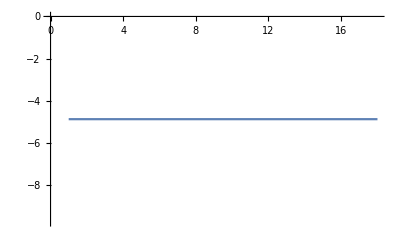

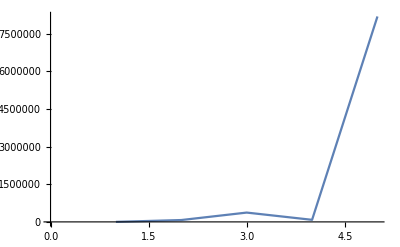

```mathematica
ListLinePlot[psiisol[[All,6]]]
ListLinePlot[resid]
```